## Reconsideration of ICPC Chapter 1

### Avoid global variables and try to make more “pure” functions by using default settings

In functional programming, a pure function is one whose only inputs are specified as arguments and whose only consequence is the value returned (no side effects).

In ICPC 1, we used some “global” variables in the definition of the PIB energy levels:

```mathematica
energy1DPIB[n_,L_]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
```

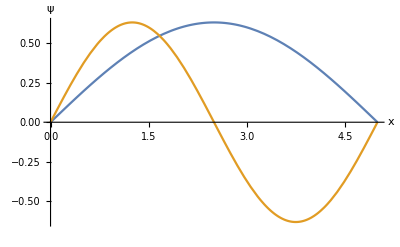

```mathematica
hbar=1; (*define variables in atomic units*)
m=1;(*set m=1 me, i.e., units of electron mass, me*)
L=5; (*set L=5 a0, i.e., units of Bohr radii, a0*)
g1=Plot[
{psi1DPIB[1,x,L],psi1DPIB[2,x,L]},
{x,0,L},AxesLabel->{"x","ψ"}]
```

A better way might be to make these arguments of the function so that it only depends on the input and not the global variables. To the extent that we often use m = 1, and hbar = 1 (in the atomic units scheme), these might be given default parameters:

```mathematica
Clear[energy1DPIB]
energy1DPIB[n_,L_,m_:1,hbar_:5]:=(hbar^2*Pi^2*n^2)/(2*m*L^2);
```

### Emphasize a more “functional” approach to 1.5.2—use Maps instead of Do loops.

In ICPC we take a procedural approach because it corresponds to common idioms in more procedurally oriented programming languages (like Python, MATLAB, etc.).  To repeat a process we often use a Do loop to sample the wavefunction:

```mathematica
(*pre-req functions*)
psi1DPIB[n_,x_,L_]:=Sqrt[2/L]*Sin[n*Pi*x/L];
psiSquared1DPIB[n_,x_,L_]:=Conjugate[psi1DPIB[n,x,L]]*psi1DPIB[n,x,L];

(*implementation in 1.5.2*)
L=5;
acceptedPoints={};
Do[
If[psiSquared1DPIB[1,x=RandomReal[{0,L}],L]≥RandomReal[{0,0.5}],AppendTo[acceptedPoints,x]
]
,{10^5}] //AbsoluteTiming
```

{7.02755,Null}

This is similar to how one would implement a process like this in other procedural programming languages like C, Python, Fortran, etc.  

A more functional way to approach this is to first define a function that takes one point as input—if it is accepted, it is returned, otherwise we return Nothing.

```mathematica
accepted[x_]:=If[
psiSquared1DPIB[1,x,L]≥RandomReal[{0,0.5}] (*test condition*),
x, (*return if true*)
Nothing (*return if false*)]

Table[ accepted[2], {10}] //Length (*observe how not all 10 are accepted!*)
```

7

Then the function is applied to a list of random numbers:

```mathematica
acceptedPoints=accepted/@RandomReal[{0,L},10^5];//AbsoluteTiming
```

{2.82185,Null}

(AbsoluteTiming is applied to show how in addition to being more idiomatic in Mathematica and providing a simpler program code, it is often significantly faster.)

Another approach is to change the attributes of functions so that they apply to lists, this is done using the SetAttributes function.  This is often slightly faster than Map:

```mathematica
SetAttributes[accepted,Listable]

accepted@RandomReal[{0,L},10^5];//AbsoluteTiming
```

{2.80545,Null}

Instead of an If statement, one can also use Select to pick elements from a list

```mathematica
accepted2[x_List]:=Select[x,psiSquared1DPIB[1,#,L]≥RandomReal[{0,0.5}]&]

accepted2@RandomReal[{0,L},10^5]; //AbsoluteTiming
```

{2.71837,Null}

Perhaps faster if we generate batches of random numbers?

```mathematica
accepted3[x_List]:=With[
{randoms=RandomReal[{0,0.5},Length[x]]},
Select[
Transpose[{x,randoms}], (*list of pairs*)
psiSquared1DPIB[1,#[[1]],L]>=#[[2]]&]][[All,1]]

accepted3@RandomReal[{0,L},10^5];//AbsoluteTiming
```

{2.74825,Null}

Although in some situations (particularly when using parallelization) this can deliverable a modest performance improvement, this is not realized in this simple case, and the added complexity of dealing with a batch of numbers does not warrant its use.

Finally, we might try the approach of using the Sow and Reap functionality :

```mathematica
accepted4[x_]:=If[
psiSquared1DPIB[1,x,L]≥RandomReal[{0,0.5}] (*test condition*),
Sow[x] (*sow the accepted value*)]

acceptedPoints=Reap[accepted4/@RandomReal[{0,L},10^5]];//AbsoluteTiming
```

{2.76017,Null}

In the end, all of these functional approaches take about the same amount of time and are significantly faster than the procedural approach.

Last edited: 31 January 2023